```mathematica
With[{root=9148},Labeled[MatrixForm[allGraphs5[root,"matrix"]],ShowGraph[allGraphs5,root]]->Multicolumn[Table[Labeled[MatrixForm[allGraphs5[k,"matrix"]],ShowGraph[allGraphs5,k]],{k,root//Connections}]]]
```

(2 | 0 | 1 | 1 | 0
0 | 2 | 1 | 1 | 2
1 | 1 | 2 | 2 | 1
1 | 1 | 2 | 2 | 1
0 | 2 | 1 | 1 | 2)-Graphics-9148→(2 | 0 | 0 | 0 | 0
0 | 2 | 1 | 1 | 2
0 | 1 | 2 | 2 | 1
0 | 1 | 2 | 2 | 1
0 | 2 | 1 | 1 | 2)-Graphics-400 | (2 | 0 | 1 | 1 | 0
0 | 2 | 1 | 1 | 1
1 | 1 | 2 | 2 | 1
1 | 1 | 2 | 2 | 1
0 | 1 | 1 | 1 | 2)-Graphics-9121 | (2 | 1 | 1 | 1 | 1
1 | 2 | 1 | 1 | 2
1 | 1 | 2 | 2 | 1
1 | 1 | 2 | 2 | 1
1 | 2 | 1 | 1 | 2)-Graphics-29560 | (2 | 2 | 1 | 1 | 2
2 | 2 | 1 | 1 | 2
1 | 1 | 2 | 2 | 1
1 | 1 | 2 | 2 | 1
2 | 2 | 1 | 1 | 2)-Graphics-49972
(2 | 0 | 1 | 1 | 0
0 | 2 | 0 | 0 | 2
1 | 0 | 2 | 2 | 0
1 | 0 | 2 | 2 | 0
0 | 2 | 0 | 0 | 2)-Graphics-8820 | (2 | 0 | 1 | 1 | 0
0 | 2 | 1 | 1 | 2
1 | 1 | 2 | 0 | 1
1 | 1 | 0 | 2 | 1
0 | 2 | 1 | 1 | 2)-Graphics-9130 | (2 | 1 | 1 | 1 | 1
1 | 2 | 2 | 2 | 2
1 | 2 | 2 | 2 | 2
1 | 2 | 2 | 2 | 2
1 | 2 | 2 | 2 | 2)-Graphics-29888 | 
(2 | 0 | 1 | 1 | 0
0 | 2 | 1 | 1 | 0
1 | 1 | 2 | 2 | 1
1 | 1 | 2 | 2 | 1
0 | 0 | 1 | 1 | 2)-Graphics-9094 | (2 | 0 | 1 | 1 | 0
0 | 2 | 1 | 1 | 2
1 | 1 | 2 | 1 | 1
1 | 1 | 1 | 2 | 1
0 | 2 | 1 | 1 | 2)-Graphics-9139 | (2 | 1 | 2 | 2 | 1
1 | 2 | 1 | 1 | 2
2 | 1 | 2 | 2 | 1
2 | 1 | 2 | 2 | 1
1 | 2 | 1 | 1 | 2)-Graphics-38308 |

```mathematica
SimpleGraph[g3, VertexLabels->Table[k->Placed[Magnify[Framed[allGraphs3[k,"graph"],Background->LightYellow],.7],Center],{k,Keys[allGraphs3]}],GraphLayout->"CircularEmbedding",
GraphHighlight->MakePath[FindShortestPath[g3,0,K3Key]],GraphHighlightStyle->"Thick"]
```

-Graphics-

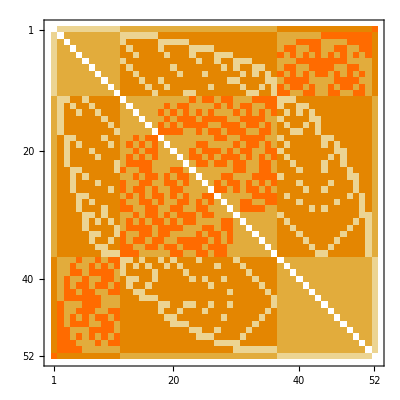
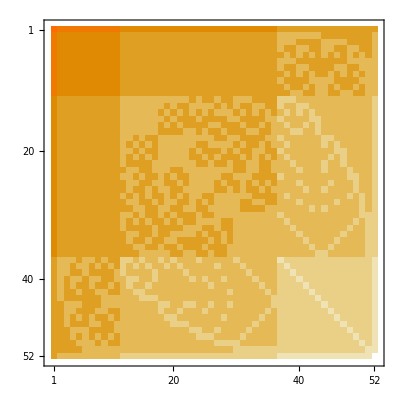
{{-Graphics-E→E,-Graphics-E→C},{-Graphics-C→E,-Graphics-C→C}}

```mathematica
Table[
Labeled[MatrixPlot[Table[GraphDistance[g,from,to],{from,Bases[base1,"AtomKeys"]},{to,Bases[base2,"AtomKeys"]}]],base1->base2],
{base1,{"E","C"}},{base2,{"E","C"}}]
```

```mathematica
Map[ShowGraph[allGraphs5,#]&,FindShortestPath[g,29524,59048]]
```

{-Graphics-29524,-Graphics-30253,-Graphics-32441,-Graphics-39014,-Graphics-59048}

```mathematica
Map[ShowGraph[allGraphs5,#]&,FindShortestPath[g,0,29524]]
```

{-Graphics-0,-Graphics-1,-Graphics-4,-Graphics-13,-Graphics-391,-Graphics-364,-Graphics-30253,-Graphics-29524}

```mathematica
Map[ShowGraph[allGraphs5,#]&,FindShortestPath[g,starKey,lambdaKey]]
```

{-Graphics-8859,-Graphics-30001,-Graphics-30262,-Graphics-23608,-Graphics-20665}

```mathematica
Map[ShowGraph[allGraphs5,#]&,FindShortestPath[g,lambdaKey,K5Key]]
```

{-Graphics-20665,-Graphics-35977,-Graphics-36004,-Graphics-36085,-Graphics-29524}